```mathematica
1/2 + 5! - Sin[Pi/2]
Pi^E  
N[Pi^E,30](* This is the numerical approx function *)
```

239/2

π^ⅇ

22.4591577183610454734271522045

Algebra (Solving Equations)

```mathematica
Solve[3x^2 + 5x -1 == 0,x]
```

{{x→1/6 (-5-√37)},{x→1/6 (-5+√37)}}

```mathematica
Solve[a x^2 + b x +c ==0,x]
```

{{x→(-b-√(b^2-4 a c))/(2 a)},{x→(-b+√(b^2-4 a c))/(2 a)}}

CALCULUS

```mathematica
f[x_] := Sin[2 x -1]*Cos[3 x + 2]
```

```mathematica
f[4]
```

Cos[14] Sin[7]

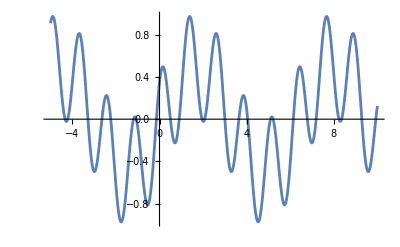

```mathematica
Plot[f[x],{x,-5,10}]
```

```mathematica
Integrate[f[x],x]
```

1/10 (5 Cos[3+x]-Cos[1+5 x])

```mathematica
Integrate[f[x],{x,0,5 Pi}]
```

1/5 (Cos[1]-5 Cos[3])

```mathematica
∫_0^(5π) f[x]ⅆx
```

1/5 (Cos[1]-5 Cos[3])

SCIENCE 
ASTRONOMY

```mathematica
g[x_] := x*E^(-A*x)*Sin[q*x]
g[2]
```

2 ⅇ^(-2 A) Sin[2 q]

```mathematica
Integrate[g[x],{x,0,Infinity}]
```

ConditionalExpression[(2 A q)/((A^2+q^2)^2), Abs[Im[q]]<Re[A]]